```mathematica
Clear["Global`*"];
ssx1i={};
ssx1d={};
ssx2i={};
ssx2d={};
ssx3i={};
ssx3d={};
ssx4i={};
ssx4d={};
ssx5i={};
ssx5d={};
ssx6i={};
ssx6d={};
ssin={};
(* Initialize all the equations and parameters *)
sTot=6.943934962;eTot=5.306064244;
dEs={D[x1[t],t]==-k1*x1[t]*x3[t]-k4*x1[t]*x4[t]+k2*x5[t]+k5*x6[t]+k7*x2[t],D[x2[t],t]==k3*x5[t]+k6*x6[t]-k7*x2[t],D[x3[t],t]==-k1*x1[t]*x3[t]+k2*x5[t]+k3*x5[t]-k8*x3[t]+k9*x4[t],D[x4[t],t]==-k4*x1[t]*x4[t]+k5*x6[t]+k6*x6[t]+k8*x3[t]-k9*x4[t],D[x5[t],t]==k1*x1[t]*x3[t]-k2*x5[t]-k3*x5[t]-k10*x5[t]+k11*x6[t],D[x6[t],t]==k4*x1[t]*x4[t]-k5*x6[t]-k6*x6[t]+k10*x5[t]-k11*x6[t]};
invaEs={x1[t]+x2[t]+x5[t]+x6[t]==sTot,x3[t]+x4[t]+x5[t]+x6[t]==eTot};
icEs={x1[0]==sTot,x2[0]==0,x3[0]==eTot,x4[0]==0,x5[0]==0,x6[0]==0};
(*params = {k1->184.8681819,k2->0.01489431477,k3->177.5280007,k4->60.26409666,k5->1.873817423,k6->0.2608688883,k7->1.57210279,k8->0.02405645734,k9->1.411107556,k10->82.77297468,k11->0.02087603873};*)
(* Get the steady state first *)
tf=50000;
input=184;
params = {k1->input,k2->0.01489431477,k3->177.5280007,k4->60.26409666,k5->1.873817423,k6->0.2608688883,k7->1.57210279,k8->0.02405645734,k9->1.411107556,k10->82.77297468,k11->0.02087603873};

sol=NDSolve[{dEs,icEs}/.params,{x1,x2,x3,x4,x5,x6},{t,0,tf}];

newIC={x1[0]==Evaluate[x1[tf]/.sol][[1]],x2[0]==Evaluate[x2[tf]/.sol][[1]],x3[0]==Evaluate[x3[tf]/.sol][[1]],x4[0]==Evaluate[x4[tf]/.sol][[1]],x5[0]==Evaluate[x5[tf]/.sol][[1]],x6[0]==Evaluate[x6[tf]/.sol][[1]]};

For[i=0,i≤2000,i++,
tf=50000;
input=184+i*0.001;
params = {k1->input,k2->0.01489431477,k3->177.5280007,k4->60.26409666,k5->1.873817423,k6->0.2608688883,k7->1.57210279,k8->0.02405645734,k9->1.411107556,k10->82.77297468,k11->0.02087603873};
newIC={x1[0]==Evaluate[x1[tf]/.sol][[1]],x2[0]==Evaluate[x2[tf]/.sol][[1]],x3[0]==Evaluate[x3[tf]/.sol][[1]],x4[0]==Evaluate[x4[tf]/.sol][[1]],x5[0]==Evaluate[x5[tf]/.sol][[1]],x6[0]==Evaluate[x6[tf]/.sol][[1]]};

sol=NDSolve[{dEs,newIC}/.params,{x1,x2,x3,x4,x5,x6},{t,0,tf}];

(*If[Abs[Evaluate[x1'[tf]/.sol][[1]]]≤0.001&&Abs[Evaluate[x1''[tf]/.sol][[1]]]≤0.001&&Abs[Evaluate[x2'[tf]/.sol][[1]]]≤0.001&&Abs[Evaluate[x2''[tf]/.sol][[1]]]≤0.001&&Abs[Evaluate[x3'[tf]/.sol][[1]]]≤0.001&&Abs[Evaluate[x3''[tf]/.sol][[1]]]≤0.001&&Abs[Evaluate[x4'[tf]/.sol][[1]]]≤0.001&&Abs[Evaluate[x4''[tf]/.sol][[1]]]≤0.001&&Abs[Evaluate[x5'[tf]/.sol][[1]]]≤0.001&&Abs[Evaluate[x5''[tf]/.sol][[1]]]≤0.001&&Abs[Evaluate[x6'[tf]/.sol][[1]]]≤0.001&&Abs[Evaluate[x6''[tf]/.sol][[1]]]≤0.001,*) 
ssx1i=Append[ssx1i,Evaluate[x1[tf]/.sol][[1]]]; 
ssx2i=Append[ssx2i,Evaluate[x2[tf]/.sol][[1]]];ssx3i=Append[ssx3i,Evaluate[x3[tf]/.sol][[1]]];ssx4i=Append[ssx4i,Evaluate[x4[tf]/.sol][[1]]];ssx5i=Append[ssx5i,Evaluate[x5[tf]/.sol][[1]]];ssx6i=Append[ssx6i,Evaluate[x6[tf]/.sol][[1]]]
(*];*)
];

For[i=0,i≤2000,i++,
tf=50000;
input=186-i*0.001;
params = {k1->input,k2->0.01489431477,k3->177.5280007,k4->60.26409666,k5->1.873817423,k6->0.2608688883,k7->1.57210279,k8->0.02405645734,k9->1.411107556,k10->82.77297468,k11->0.02087603873};
newIC={x1[0]==Evaluate[x1[tf]/.sol][[1]],x2[0]==Evaluate[x2[tf]/.sol][[1]],x3[0]==Evaluate[x3[tf]/.sol][[1]],x4[0]==Evaluate[x4[tf]/.sol][[1]],x5[0]==Evaluate[x5[tf]/.sol][[1]],x6[0]==Evaluate[x6[tf]/.sol][[1]]};

sol=NDSolve[{dEs,newIC}/.params,{x1,x2,x3,x4,x5,x6},{t,0,tf}];

(*If[Abs[Evaluate[x1'[tf]/.sol][[1]]]≤0.001&&Abs[Evaluate[x1''[tf]/.sol][[1]]]≤0.001&&Abs[Evaluate[x2'[tf]/.sol][[1]]]≤0.001&&Abs[Evaluate[x2''[tf]/.sol][[1]]]≤0.001&&Abs[Evaluate[x3'[tf]/.sol][[1]]]≤0.001&&Abs[Evaluate[x3''[tf]/.sol][[1]]]≤0.001&&Abs[Evaluate[x4'[tf]/.sol][[1]]]≤0.001&&Abs[Evaluate[x4''[tf]/.sol][[1]]]≤0.001&&Abs[Evaluate[x5'[tf]/.sol][[1]]]≤0.001&&Abs[Evaluate[x5''[tf]/.sol][[1]]]≤0.001&&Abs[Evaluate[x6'[tf]/.sol][[1]]]≤0.001&&Abs[Evaluate[x6''[tf]/.sol][[1]]]≤0.001,*) 
ssx1d=Append[ssx1d,Evaluate[x1[tf]/.sol][[1]]]; 
ssx2d=Append[ssx2d,Evaluate[x2[tf]/.sol][[1]]];ssx3d=Append[ssx3d,Evaluate[x3[tf]/.sol][[1]]];ssx4d=Append[ssx4d,Evaluate[x4[tf]/.sol][[1]]];ssx5d=Append[ssx5d,Evaluate[x5[tf]/.sol][[1]]];ssx6d=Append[ssx6d,Evaluate[x6[tf]/.sol][[1]]]
(*];*)
];
```

```mathematica
k1List=Range[180,190,0.1]
```

{180.,180.1,180.2,180.3,180.4,180.5,180.6,180.7,180.8,180.9,181.,181.1,181.2,181.3,181.4,181.5,181.6,181.7,181.8,181.9,182.,182.1,182.2,182.3,182.4,182.5,182.6,182.7,182.8,182.9,183.,183.1,183.2,183.3,183.4,183.5,183.6,183.7,183.8,183.9,184.,184.1,184.2,184.3,184.4,184.5,184.6,184.7,184.8,184.9,185.,185.1,185.2,185.3,185.4,185.5,185.6,185.7,185.8,185.9,186.,186.1,186.2,186.3,186.4,186.5,186.6,186.7,186.8,186.9,187.,187.1,187.2,187.3,187.4,187.5,187.6,187.7,187.8,187.9,188.,188.1,188.2,188.3,188.4,188.5,188.6,188.7,188.8,188.9,189.,189.1,189.2,189.3,189.4,189.5,189.6,189.7,189.8,189.9,190.}

```mathematica
Length[k1List]
```

101

```mathematica
Length[ssx2i]
```

101

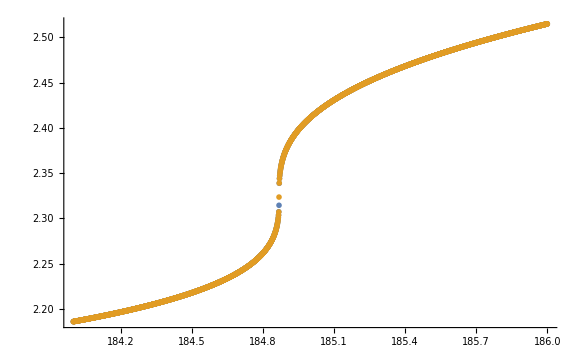

```mathematica
ListPlot[{Transpose@{Range[184,186,0.001],ssx2i},Transpose@{Range[184,186,0.001],Reverse[ssx2d]}}]
```

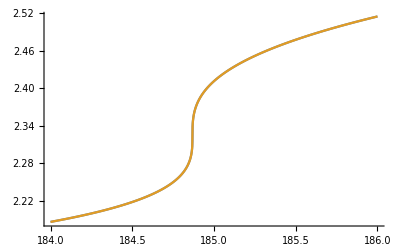

```mathematica
ListLinePlot[{Transpose@{Range[184,186,0.001],ssx2i},Transpose@{Range[184,186,0.001],Reverse[ssx2d]}}]
```

```mathematica
ListPlot[{{k1List,ssx2i},{k1List,Reverse[ssx2d]}}]
```

ListPlot::lpn: {{{180., 180.1, 180.2, 180.3, 180.4, 180.5, 180.6, 180.7, 180.8, 180.9, 181., 181.1, 181.2, 181.3, 181.4, 181.5, 181.6, 181.7, 181.8, 181.9, 182., 182.1, 182.2, 182.3, 182.4, 182.5, 182.6, 182.7, 182.8, 182.9, 183., 183.1, 183.2, 183.3, 183.4, 183.5, 183.6, 183.7, 183.8, 183.9, 184., 184.1, 184.2, 184.3, 184.4, 184.5, 184.6, 184.7, 184.8, 184.9, « 51 »}, {2.12922, « 49 », « 51 »}}, « 1 »} is not a list of numbers or pairs of numbers.

ListPlot[{{{180.,180.1,180.2,180.3,180.4,180.5,180.6,180.7,180.8,180.9,181.,181.1,181.2,181.3,181.4,181.5,181.6,181.7,181.8,181.9,182.,182.1,182.2,182.3,182.4,182.5,182.6,182.7,182.8,182.9,183.,183.1,183.2,183.3,183.4,183.5,183.6,183.7,183.8,183.9,184.,184.1,184.2,184.3,184.4,184.5,184.6,184.7,184.8,184.9,185.,185.1,185.2,185.3,185.4,185.5,185.6,185.7,185.8,185.9,186.,186.1,186.2,186.3,186.4,186.5,186.6,186.7,186.8,186.9,187.,187.1,187.2,187.3,187.4,187.5,187.6,187.7,187.8,187.9,188.,188.1,188.2,188.3,188.4,188.5,188.6,188.7,188.8,188.9,189.,189.1,189.2,189.3,189.4,189.5,189.6,189.7,189.8,189.9,190.},{2.12922,2.0951,2.09588,2.09725,2.09865,2.10008,2.10153,2.103,2.1045,2.10602,2.10758,2.10916,2.11077,2.11242,2.1141,2.11581,2.11756,2.11935,2.12118,2.12305,2.12496,2.12693,2.12894,2.13101,2.13314,2.13532,2.13757,2.13989,2.14229,2.14476,2.14733,2.14998,2.15274,2.15561,2.15861,2.16174,2.16501,2.16846,2.17209,2.17594,2.18003,2.18439,2.18908,2.19415,2.19968,2.20576,2.21252,2.22016,2.22892,2.2392,2.25158,2.26698,2.28686,2.31343,2.34912,2.39339,2.43715,2.46854,2.4868,2.49795,2.50622,2.51334,2.51987,2.52603,2.53187,2.53746,2.54283,2.54799,2.55298,2.5578,2.56247,2.56701,2.57142,2.57573,2.57992,2.58402,2.58802,2.59194,2.59577,2.59953,2.60322,2.60684,2.6104,2.61389,2.61733,2.62071,2.62404,2.62732,2.63055,2.63373,2.63687,2.63997,2.64302,2.64604,2.64902,2.65196,2.65487,2.65774,2.66058,2.66339,2.66617}},{{180.,180.1,180.2,180.3,180.4,180.5,180.6,180.7,180.8,180.9,181.,181.1,181.2,181.3,181.4,181.5,181.6,181.7,181.8,181.9,182.,182.1,182.2,182.3,182.4,182.5,182.6,182.7,182.8,182.9,183.,183.1,183.2,183.3,183.4,183.5,183.6,183.7,183.8,183.9,184.,184.1,184.2,184.3,184.4,184.5,184.6,184.7,184.8,184.9,185.,185.1,185.2,185.3,185.4,185.5,185.6,185.7,185.8,185.9,186.,186.1,186.2,186.3,186.4,186.5,186.6,186.7,186.8,186.9,187.,187.1,187.2,187.3,187.4,187.5,187.6,187.7,187.8,187.9,188.,188.1,188.2,188.3,188.4,188.5,188.6,188.7,188.8,188.9,189.,189.1,189.2,189.3,189.4,189.5,189.6,189.7,189.8,189.9,190.},{2.09591,2.09729,2.0987,2.10013,2.10158,2.10306,2.10456,2.10609,2.10765,2.10924,2.11086,2.11252,2.1142,2.11593,2.11769,2.11949,2.12133,2.12321,2.12515,2.12713,2.12917,2.13126,2.13341,2.13563,2.13792,2.14028,2.14272,2.14525,2.14788,2.15061,2.15346,2.15643,2.15955,2.16284,2.16631,2.16999,2.17394,2.17825,2.1832,2.18957,2.19958,2.21763,2.24759,2.28562,2.32258,2.35357,2.3785,2.39872,2.41554,2.42988,2.4424,2.45353,2.46357,2.47275,2.48123,2.48912,2.49653,2.5035,2.51012,2.51641,2.52243,2.5282,2.53374,2.53908,2.54423,2.54922,2.55406,2.55876,2.56333,2.56777,2.57211,2.57634,2.58047,2.58452,2.58847,2.59235,2.59615,2.59987,2.60353,2.60713,2.61066,2.61413,2.61755,2.62091,2.62423,2.62749,2.63071,2.63388,2.63701,2.64009,2.64314,2.64615,2.64912,2.65206,2.65496,2.65782,2.66066,2.66346,2.66624,2.66892,2.66617}}}]